### functions

```mathematica
matrixPower[matrix_,power_]:=Module[{evsTransposed=Transpose[Eigenvectors[matrix]],eas=Eigenvalues[matrix]+1.*^-9},
Return[evsTransposed.DiagonalMatrix[eas^power].Inverse[evsTransposed]]]
(*overlapSimilarity[cov1_,cov2_]:=Module[{sqrtCov1=matrixPower[cov1,1/2],sqrtCov2=matrixPower[cov2,1/2]},Return[Tr[sqrtCov1.sqrtCov2]/Norm[sqrtCov1,"Frobenius"]/Norm[sqrtCov2,"Frobenius"]]];
weight=Identity;*)
overlapSimilarity[cov1_,cov2_]:=Return[Tr[cov1.cov2]/Norm[cov1,"Frobenius"]/Norm[cov2,"Frobenius"]];
weight=Function[{x},x^2];
```

```mathematica
covGeneration[eas_,evs_]:=Module[{evsNormalized=ConstantArray[0.,Dimensions[evs]],evN=Length[evs]},Do[evsNormalized[[evIdx]]=Normalize[evs[[evIdx]]],{evIdx,evN}];Return[Transpose[evsNormalized].DiagonalMatrix[eas].evsNormalized]]
```

### demo

#### 1d data

```mathematica
plotN=8;covs=Table[{covGeneration[{1},{{1,0,0}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1},{{Cos[angle],Sin[angle],0}}]+1*^-9*IdentityMatrix[3]},{angle,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[angleIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[angleIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{angleIdx,0,plotN}];
quantifications=Table[{Cos[angleIdx*Pi/plotN],(Cos[angleIdx*Pi/plotN*2]+1)/2,overlapSimilarity[covs[[angleIdx+1,1]],covs[[angleIdx+1,2]]]},{angleIdx,0,plotN}]*1.;
methods={"Cos","(Cos+1)/2","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
Cos | 1. | 0.92388 | 0.707107 | 0.382683 | 0. | -0.382683 | -0.707107 | -0.92388 | -1.
(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
overlapSimilarity | 1. | 0.853553 | 0.5 | 0.146447 | 2.×10^-9 | 0.146447 | 0.5 | 0.853553 | 1.

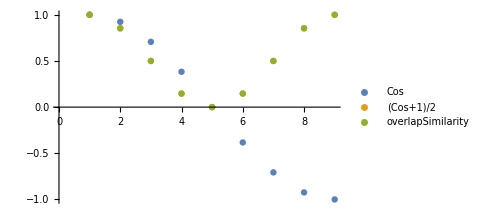

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```

#### 2d data one-axis-aligned

```mathematica
plotN=8;sharedVar=(*0.*)3;covs=Table[{covGeneration[{1,sharedVar},{{1,0,0},{0,0,1}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1,sharedVar},{{Cos[phi],Sin[phi],0},{0,0,1}}]+1*^-9*IdentityMatrix[3]},{phi,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{phiIdx,0,plotN}];
quantifications=Table[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,Total[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,1}*weight[{1,sharedVar}]]/Total[weight[{1,sharedVar}]],overlapSimilarity[covs[[phiIdx+1,1]],covs[[phiIdx+1,2]]]},{phiIdx,0,plotN}];
methods={"CosSimilarity:(Cos+1)/2","abDiag^2WeightedCosSimilarity/totVar","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
CosSimilarity:(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
abDiag^2WeightedCosSimilarity/totVar | 1. | 0.985355 | 0.95 | 0.914645 | 0.9 | 0.914645 | 0.95 | 0.985355 | 1.
overlapSimilarity | 1. | 0.985355 | 0.95 | 0.914645 | 0.9 | 0.914645 | 0.95 | 0.985355 | 1.

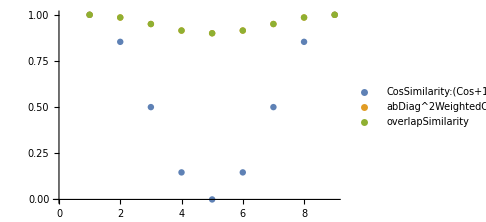

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```

#### 2d data rotate-by-r-hat

```mathematica
plotN=8;
sharedVar=(*0.*)3;
theta=Pi/6;
covs=Table[{covGeneration[{1,sharedVar},{{1,0,0},{0,0,1}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1,sharedVar},{{Cos[phi],Sin[phi],0},{Sin[phi]Sin[theta],-Cos[phi]Sin[theta],Cos[theta]}}]+1*^-9*IdentityMatrix[3]},{phi,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{phiIdx,0,plotN}];
quantifications=Table[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,Total[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,(Cos[theta*2]+1)/2*1.}*weight[{1,sharedVar}]]/Total[weight[{1,sharedVar}]],overlapSimilarity[covs[[phiIdx+1,1]],covs[[phiIdx+1,2]]]},{phiIdx,0,plotN}];
methods={"CosSimilarity:(Cos+1)/2","totVar^2WeightedCosSimilarity/totVar","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
CosSimilarity:(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
totVar^2WeightedCosSimilarity/totVar | 0.775 | 0.760355 | 0.725 | 0.689645 | 0.675 | 0.689645 | 0.725 | 0.760355 | 0.775
overlapSimilarity | 0.775 | 0.771339 | 0.7625 | 0.753661 | 0.75 | 0.753661 | 0.7625 | 0.771339 | 0.775

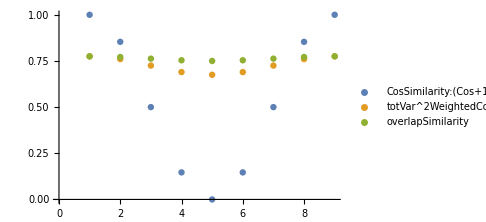

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```

#### 2d data rotate-by-phi-hat

```mathematica
plotN=8;
sharedVar=(*0.*)3;
theta=Pi/6;
covs=Table[{covGeneration[{1,sharedVar},{{1,0,0},{0,0,1}}]+1.*^-9*IdentityMatrix[3],covGeneration[{1,sharedVar},{{Cos[phi]Cos[theta],Sin[phi]Cos[theta],Sin[theta]},{Cos[phi]Sin[theta],Sin[phi]Sin[theta],Cos[theta]}}]+1*^-9*IdentityMatrix[3]},{phi,0,Pi,Pi/plotN}];
plots=Table[ListPointPlot3D[{RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,1]]],500],RandomVariate[MultinormalDistribution[{0,0,0},covs[[phiIdx+1,2]]],500]},PlotRange->Table[{-4,4},3],AspectRatio->1],{phiIdx,0,plotN}];
quantifications=Table[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,Total[{(Cos[phiIdx*Pi/plotN*2]+1)/2*1.,(Cos[theta*2]+1)/2*1.}*weight[{1,sharedVar}]]/Total[weight[{1,sharedVar}]],overlapSimilarity[covs[[phiIdx+1,1]],covs[[phiIdx+1,2]]]},{phiIdx,0,plotN}];
methods={"CosSimilarity:(Cos+1)/2","totVar^2WeightedCosSimilarity/totVar","overlapSimilarity"};
```

```mathematica
Grid[Transpose[ArrayFlatten[{{{{"plot"}},{methods}},{Transpose[{plots}],quantifications}}]],Frame->All]
```

plot | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
CosSimilarity:(Cos+1)/2 | 1. | 0.853553 | 0.5 | 0.146447 | 0. | 0.146447 | 0.5 | 0.853553 | 1.
totVar^2WeightedCosSimilarity/totVar | 0.775 | 0.760355 | 0.725 | 0.689645 | 0.675 | 0.689645 | 0.725 | 0.760355 | 0.775
overlapSimilarity | 0.747409 | 0.729167 | 0.685125 | 0.641084 | 0.622841 | 0.641084 | 0.685125 | 0.729167 | 0.747409

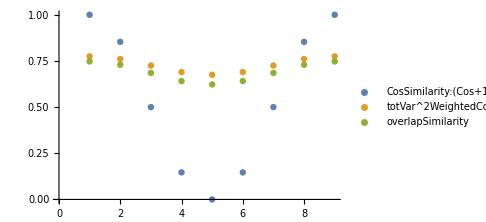

```mathematica
ListPlot[Transpose[quantifications],PlotLegends->methods,ImageSize->Medium]
```

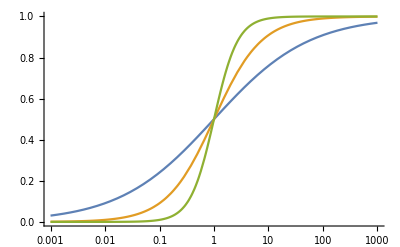

```mathematica
LogLinearPlot[{Sqrt[sharedVar]/(1+Sqrt[sharedVar]),sharedVar/(1+sharedVar),sharedVar^2/(1+sharedVar^2)(*,Sqrt[sharedVar^2/(1+sharedVar^2)]*)},{sharedVar,1*^-3,1*^3}]
```